```mathematica
<<D:\\Economics\Courses\MGSC533\2021\Math\Lags\ARlags.m;
```

```mathematica
<<D:\\Economics\Courses\MGSC533\2021\Data\BRLpCADpGBPpJPYpMXNpNOKpTRLpUSD.txt;
```

```mathematica
(*  The first example has no lags.  It is a standard AR process.   *)
```

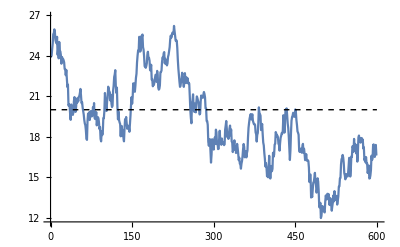

```mathematica
PriceSequenceGraphLags[{0, 0, 0, 0, 0, 0, 0, 0, 0},0.02,24,20,600,0.5, True]
```

```mathematica
(*  The next example includes three lags.                         *)
```

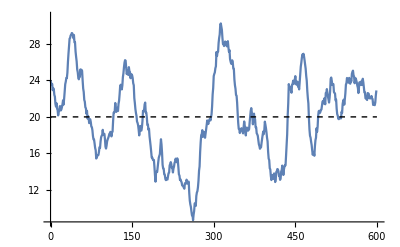

```mathematica
PriceSequenceGraphLags[{0.3, 0.2, 0.1, 0, 0, 0, 0, 0, 0},0.02,24,20,600,0.5, True]
```

```mathematica
Off[General::munfl]
```

```mathematica
(*  The next function creates a sequence with lags and the one      *)
(*  that follows it estimates the parameters of the model.          *)
```

```mathematica
c02n600Lags123 = PriceSequenceLags[{0.3, 0.2, 0.1, 0, 0, 0, 0, 0, 0},0.02,24,20,600,0.5];
```

```mathematica
LagTestn[Transpose[c02n600Lags123][[2]],9]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.497323 | 0.123477 | 4.02767 | 0.0000638374
a | 0.0258786 | 0.00633446 | 4.08538 | 0.0000502119
b1 | 0.297455 | 0.0406818 | 7.31173 | 8.8155×10^-13
b2 | 0.211729 | 0.0424417 | 4.9887 | 8.04888×10^-7
b3 | 0.0466305 | 0.0434073 | 1.07425 | 0.283156
b4 | -0.016512 | 0.0434261 | -0.380233 | 0.703912
b5 | 0.0204845 | 0.043399 | 0.472005 | 0.637101
b6 | 0.0478726 | 0.0433304 | 1.10483 | 0.269693
b7 | 0.0501695 | 0.0433704 | 1.15677 | 0.247845
b8 | 0.0881113 | 0.0427407 | 2.06153 | 0.0396983
b9 | -0.0920586 | 0.0414215 | -2.22249 | 0.0266361,0.231251,19.2724}

```mathematica
(*  If we select only the lags that were significant in the      *)
(*  previous regression report we should recover the lags        *)
(*  that were present in the data generating process.            *)
```

```mathematica
LagTestn[Transpose[c02n600Lags123][[2]],3]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.429671 | 0.112794 | 3.80934 | 0.000153917
a | 0.022355 | 0.00575382 | 3.88525 | 0.000113784
b1 | 0.298149 | 0.0406002 | 7.34353 | 6.93047×10^-13
b2 | 0.21445 | 0.0416671 | 5.14676 | 3.6128×10^-7
b3 | 0.0591334 | 0.0411424 | 1.43728 | 0.151166,0.212335,19.2748}

```mathematica
(*  We can take a more or less arbitrary array of lags and check to see    *)
(*  if we can detect the non-zero ones.                                    *)
```

```mathematica
c02n600Lags158 = PriceSequenceLags[{0.55, 0, 0, 0, 0.3, 0, 0, 0.1, 0},0.02,18,20,600,1];
```

```mathematica
LagTestn[Transpose[c02n600Lags158][[2]],9]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.418741 | 0.0833657 | 5.02294 | 6.7879×10^-7
a | 0.0182448 | 0.00320508 | 5.69246 | 1.99161×10^-8
b1 | 0.542324 | 0.0409652 | 13.2386 | 3.86988×10^-35
b2 | 0.0752855 | 0.0468632 | 1.60649 | 0.108711
b3 | -0.0743487 | 0.0468636 | -1.58649 | 0.113174
b4 | 0.0369617 | 0.0469204 | 0.787753 | 0.431164
b5 | 0.28725 | 0.0456424 | 6.29348 | 6.13179×10^-10
b6 | -0.0287302 | 0.0471115 | -0.609834 | 0.542211
b7 | 0.0587445 | 0.0470032 | 1.2498 | 0.211878
b8 | 0.02808 | 0.046981 | 0.597689 | 0.550281
b9 | -0.0151878 | 0.041657 | -0.364593 | 0.715549,0.58761,23.1229}

```mathematica
LagTestn[Transpose[c02n600Lags158][[2]],8]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.424254 | 0.0814397 | 5.20943 | 2.63448×10^-7
a | 0.018566 | 0.00310934 | 5.97106 | 4.10608×10^-9
b1 | 0.543182 | 0.040937 | 13.2687 | 2.7537×10^-35
b2 | 0.0717704 | 0.0467387 | 1.53557 | 0.125189
b3 | -0.0743739 | 0.0467901 | -1.58952 | 0.112487
b4 | 0.0360865 | 0.045595 | 0.791457 | 0.429
b5 | 0.283752 | 0.0455254 | 6.23283 | 8.80841×10^-10
b6 | -0.0284243 | 0.0469578 | -0.605317 | 0.545205
b7 | 0.0599125 | 0.0468868 | 1.27781 | 0.201827
b8 | 0.0211126 | 0.0416262 | 0.507194 | 0.612211,0.586596,23.1194}

```mathematica
(*  Sometimes we don't get back the signicant lags.  Sometimes     *)
(*  we might get back lags that were not in the simulation too,    *)
(*  but this example is about a missing lag.                       *)
```

```mathematica
LagTest[Transpose[c02n600Lags158][[2]],{1, 0, 0, 0, 1, 0, 0, 0, 0}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.386858 | 0.0759117 | 5.09616 | 4.6622×10^-7
a | 0.0167096 | 0.00283818 | 5.88745 | 6.55746×10^-9
b1 | 0.583215 | 0.0300698 | 19.3954 | 2.60733×10^-65
b5 | 0.300623 | 0.0313069 | 9.60245 | 2.14446×10^-20,0.579882,23.1518}

```mathematica
(*  The first thing that we can check for is to see that when all   *)
(*  lags are zero we get the same distribution of t-statistics      *)
(*  from the estimates of the adjustment rate that we get when      *)
(*  we use the model without lags.  This is a check of our          *)
(*  simulation and estimation programs, because in principle        *) 
(*  there is no difference between the programs or the estimation   *)
(*  programs.                                                       *)
```

```mathematica
(*  CALCULATE THE POWER FOR A MODEL WITH NO LAG (β = 0.0) AND       *) (*  ADJUSTMENT RATE 0.02.                                           *)
```

```mathematica
c02n600noLagsL100k= Table[PriceSequenceLags[{0, 0, 0, 0, 0, 0, 0, 0, 0},0.02,20,20,600,0.5], 100000];
```

```mathematica
c02n600noLagsL100kEst =  LagTestnDistribution[c02n600noLagsL100k,1];
```

```mathematica
(*  Make a histogram of the estimates for the first lag.           *)
```

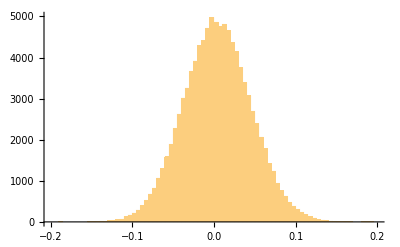

```mathematica
Histogram[Sort[c02n600noLagsL100kEst[[3, 1]]], 60, PlotRange -> {{-0.2, 0.2}, {0, 5000}}]
```

```mathematica
(*  Make a histogram of the t-statistics for the first lag.        *)
```

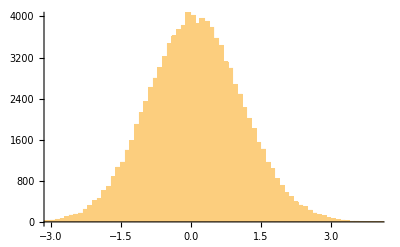

```mathematica
Histogram[Sort[c02n600noLagsL100kEst[[6, 1]]], 70, PlotRange -> {{-3, 4}, {0, 4000}}]
```

```mathematica
(*  Find the two-tailed 95% confidence interval for the             *)
(*  t-statistics associated with the estimates of the first lag.    *)
```

```mathematica
{Sort[c02n600noLagsL100kEst[[6, 1]]][[2500]], Sort[c02n600noLagsL100kEst[[6, 1]]][[97500]]}
```

{-1.85077,2.09196}

```mathematica
(*  Make a histogram of the t-statistics for the adjustment rate.  *)
```

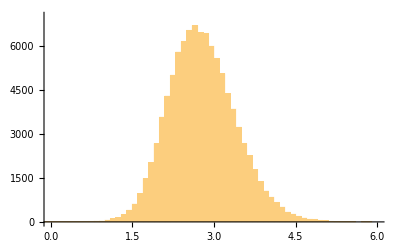

```mathematica
Histogram[Sort[c02n600noLagsL100kEst[[5]]], 60, PlotRange -> {{0, 6}, {0, 7000}}]
```

```mathematica
(*  Find the power of a test for a positive adjustment rate when      *)
(*  the adjustment rate is c = 0.02 and the sequence length n = 600   *)
(*  in the case of no lags.                                           *)
```

```mathematica
Sort[c02n600noLagsL100kEst[[5]]][[59017]]
```

2.89005

```mathematica
N[(100000 - 59017)/100000]
```

0.40983

```mathematica
(*  CALCULATE THE POWER FOR A MODEL WITH ONE LAG (β = 0.1) AND       *) (*  ADJUSTMENT RATE 0.02.                                             *)
```

```mathematica
c02n600Lag1b01L100k = Table[PriceSequenceLags[{0.1, 0, 0, 0, 0, 0, 0, 0, 0},0.02,20,20,600,0.5], 100000];
```

```mathematica
c02n600Lag1b01L100kEst = LagTestnDistribution[c02n600Lag1b01L100k,1];
```

```mathematica
(*  The power of this estimate is approximately 48.5%.  This is better   *)
(*  power than the model without a lag.  In that model we had power of   *)
(*  approximately 40.9%.                                                 *)
```

```mathematica
Sort[c02n600Lag1b01L100kEst[[5]]][[51547]]
```

2.89001

```mathematica
N[(100000 - 51547)/100000]
```

0.48453

```mathematica
(*  We can also look at how often we get t-statistics in the two-sided   *)
(*  95% confidence interval for the t-statistics on the first lag        *)(*  under the null hypothesis of no lag.  That interval is               *)
(*  (-1.866, 2.082).                                                     *)
```

```mathematica
{Sort[c02n600Lag1b01L100kEst[[6, 1]]][[1]], Sort[c02n600Lag1b01L100kEst[[6, 1]]][[32824]]}
```

{-2.01618,2.082}

```mathematica
N[(100000 - 32824)/100000]
```

0.67176

```mathematica
(*  Generate a sequence with a single lag in the first position.  *)
(*  Estimate with two lags in order to see the distribution of    *)
(*  t-statistics for the lag that is present (lag 1) and for     *)
(*  one lag that is not present (lag 2).                         *)
```

```mathematica
c02n600Lag1b01L100k= Table[PriceSequenceLags[{0.1, 0, 0, 0, 0, 0, 0, 0, 0},0.02,20,20,600,0.5], 100000];
```

```mathematica
c02n600Lag2b01L100kEst = LagTestnDistribution2[c02n600Lag1b01L100k,2];
```

```mathematica
{Sort[c02n600Lag2b01L100kEst[[6, 2]]][[2500]], Sort[c02n600Lag2b01L100kEst[[6, 2]]][[97500]]}
```

{-1.81033,1.95953}

```mathematica
{Sort[c02n600Lag2b01L100kEst[[3, 2]]][[2500]], Sort[c02n600Lag2b01L100kEst[[3, 2]]][[50000]],Sort[c02n600Lag2b01L100kEst[[3, 2]]][[97500]]}
```

{-0.0742078,0.00163526,0.0802576}

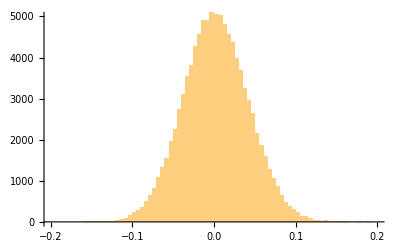

```mathematica
Histogram[Sort[c02n600Lag2b01L100kEst[[3, 2]]], 60, PlotRange -> {{-0.2, 0.2}, {0, 5000}}]
```

```mathematica
CDF[StudentTDistribution[599], -1.963932248945279]
```

0.025

```mathematica
CDF[StudentTDistribution[599], 1.963932248945279]
```

0.975

```mathematica
(*  CALCULATE THE POWER FOR A MODEL WITH ONE LAG (β = 0.2) AND       *) (*  ADJUSTMENT RATE 0.02.                                             *)
```

```mathematica
c02n600Lag1b02L100k = Table[PriceSequenceLags[{0.2, 0, 0, 0, 0, 0, 0, 0, 0},0.02,20,20,600,0.5], 100000];
```

```mathematica
c02n600Lag1b02L100kEst = LagTestnDistribution2[c02n600Lag1b02L100k,1];
```

```mathematica
(*  All but 164 of the t-statistics associated with the lag estimates    *)
(*  are in the two-sided confidence interval for the first lag.          *)
```

```mathematica
{Sort[c02n600Lag1b02L100kEst[[6, 1]]][[1]], Sort[c02n600Lag1b02L100kEst[[6, 1]]][[164]]}
```

{0.294491,2.08041}

```mathematica
N[(100000 -164)/100000]
```

0.99836

```mathematica
(*  The power of the test for a positive adjustment rate is about 57.5%. *)
```

```mathematica
Sort[c02n600Lag1b02L100kEst[[5]]][[42515]]
```

2.89

```mathematica
N[(100000 - 42515)/100000]
```

0.57485

```mathematica
(*  CALCULATE THE POWER FOR A MODEL WITH ONE LAG (β = 0.3) AND       *) (*  ADJUSTMENT RATE 0.02.                                             *)
```

```mathematica
c02n600Lag1b03L100k = Table[PriceSequenceLags[{0.3, 0, 0, 0, 0, 0, 0, 0, 0},0.02,20,20,600,0.5], 100000];
```

```mathematica
c02n600Lag1b03L100k = Table[PriceSequenceLags[{0.3, 0, 0, 0, 0, 0, 0, 0, 0},0.02,20,20,600,0.5], 100000];
```

```mathematica
c02n600Lag1b03L100kEst = LagTestnDistribution2[c02n600Lag1b03L100k,1];
```

```mathematica
Sort[c02n600Lag1b03L100kEst[[5]]][[31198]]
```

2.89007

```mathematica
N[(100000 - 31198)/100000]
```

0.68802

```mathematica
(*  CALCULATE THE POWER FOR A MODEL WITH ONE LAG (β = 0.4) AND       *) (*  ADJUSTMENT RATE 0.02.                                             *)
```

```mathematica
c02n600Lag1b04L100k = Table[PriceSequenceLags[{0.4, 0, 0, 0, 0, 0, 0, 0, 0},0.02,20,20,600,0.5], 100000];
```

```mathematica
c02n600Lag1b04L100kEst = LagTestnDistribution2[c02n600Lag1b04L100k,1];
```

```mathematica
Sort[c02n600Lag1b04L100kEst[[5]]][[18830]]
```

2.89

```mathematica
N[(100000 - 18830)/100000]
```

0.8117

```mathematica
(*  Calculate a critical value for a model with one lag (β = 0.3).      *)
```

```mathematica
c0n600Lag1b03L100k = Table[PriceSequenceLags[{0.3, 0, 0, 0, 0, 0, 0, 0, 0},0.0,20,20,600,0.5], 100000];
```

```mathematica
c0n600Lag1b03L100kEst = LagTestnDistribution2[c0n600Lag1b03L100k,1];
```

```mathematica
Sort[c0n600Lag1b03L100kEst[[5]]][[95000]]
```

2.88403

```mathematica
(*  CALCULATE THE POWER FOR A MODEL WITH ONE LAG (β = 0.0) AND       *) (*  ADJUSTMENT RATE 0.03.                                             *)
```

```mathematica
c03n600Lag1b0L100k = Table[PriceSequenceLags[{0, 0, 0, 0, 0, 0, 0, 0, 0},0.03,20,20,600,0.5], 100000];
```

```mathematica
c03n600Lag1b0L100kEst = LagTestnDistribution2[c03n600Lag1b0L100k,1];
```

```mathematica
Sort[c03n600Lag1b0L100kEst[[5]]][[14916]]
```

2.89007

```mathematica
(*  CALCULATE THE POWER FOR A MODEL WITH ONE LAG (β = 0.1) AND       *) (*  ADJUSTMENT RATE 0.03.                                             *)
```

```mathematica
c03n600Lag1b01L100k = Table[PriceSequenceLags[{0.1, 0, 0, 0, 0, 0, 0, 0, 0},0.03,20,20,600,0.5], 100000];
```

```mathematica
c03n600Lag1b01L100kEst = LagTestnDistribution2[c03n600Lag1b01L100k,1];
```

```mathematica
Sort[c03n600Lag1b01L100kEst[[5]]][[18846]]
```

2.89

```mathematica
N[(100000 - 18846)/100000]
```

0.81154

```mathematica
(*  CALCULATE THE POWER FOR A MODEL WITH ONE LAG (β = 0.2) AND       *) (*  ADJUSTMENT RATE 0.03.                                             *)
```

```mathematica
c03n600Lag1b02L100k = Table[PriceSequenceLags[{0.2, 0, 0, 0, 0, 0, 0, 0, 0},0.03,20,20,600,0.5], 100000];
```

```mathematica
c03n600Lag1b02L100kEst = LagTestnDistribution2[c03n600Lag1b02L100k,1];
```

```mathematica
Sort[c03n600Lag1b02L100kEst[[5]]][[11116]]
```

2.89

```mathematica
N[(100000 - 11116)/100000]
```

0.88884

```mathematica
(*  CALCULATE THE POWER FOR A MODEL WITH ONE LAG (β = 0.3) AND       *) (*  ADJUSTMENT RATE 0.03.                                             *)
```

```mathematica
c03n600Lag1b03L100k = Table[PriceSequenceLags[{0.3, 0, 0, 0, 0, 0, 0, 0, 0},0.03,20,20,600,0.5], 100000];
```

```mathematica
c03n600Lag1b03L100kEst = LagTestnDistribution2[c03n600Lag1b03L100k,1];
```

```mathematica
Sort[c03n600Lag1b03L100kEst[[5]]][[4993]]
```

2.89002

```mathematica
N[(100000 - 4993)/100000]
```

0.95007

```mathematica
(*  CALCULATE THE POWER FOR A MODEL WITH ONE LAG (β = 0.4) AND       *) (*  ADJUSTMENT RATE 0.03.                                             *)
```

```mathematica
c03n600Lag1b04L100k = Table[PriceSequenceLags[{0.4, 0, 0, 0, 0, 0, 0, 0, 0},0.03,20,20,600,0.5], 100000];
```

```mathematica
c03n600Lag1b04L100kEst = LagTestnDistribution2[c03n600Lag1b04L100k,1];
```

```mathematica
Sort[c03n600Lag1b04L100kEst[[5]]][[1619]]
```

2.89014

```mathematica
N[(100000 - 1619)/100000]
```

0.98381